```mathematica
eta[t_]:=c4/(Cos[c1 t+c2]);
x[t_]:=c4 Tan[c2+c1 t]+c3;
```

```mathematica
(*Check eom satisfied: should give constants*)
D[x[t],t]/eta[t]^2
(eta[t]D[eta[t],t]-x[t]D[x[t],t])/eta[t]^2//Simplify
```

c1/c4

-(c1 c3)/c4

```mathematica
(*check original eom*)
D[eta[t],{t,2}]-(D[eta[t],t]^2+D[x[t],t]^2)/eta[t]//Simplify
D[x[t],{t,2}]-2 D[eta[t],t]D[x[t],t]/eta[t]
```

0

0

```mathematica
solconst=Solve[{eta[0]==EA,eta[1]==EB,x[0]==XA,x[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solINI=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

```mathematica
solINI⟦1⟧/.{EA->-10,EB->-5,XA->1,XB->2}//N
solINI⟦2⟧/.{EA->-10,EB->-5,XA->1,XB->2}//N
```

{c3→39.,c4→0.+36.6606 ⅈ,c1→0.+0.679663 ⅈ,c2→1.5708+2.01037 ⅈ}

{c3→39.,c4→0.-36.6606 ⅈ,c1→0.-0.679663 ⅈ,c2→1.5708-2.01037 ⅈ}

```mathematica
par={EA->-5,EB->-5,XA->1,XB->20};
```

```mathematica
{x[t]/.solINI⟦1⟧/.par,eta[t]/.solINI⟦1⟧/.par}/.t->1/2//N
```

{10.5-9.89239×10^-16 ⅈ,-6.58965×10^-31-8.07775 ⅈ}

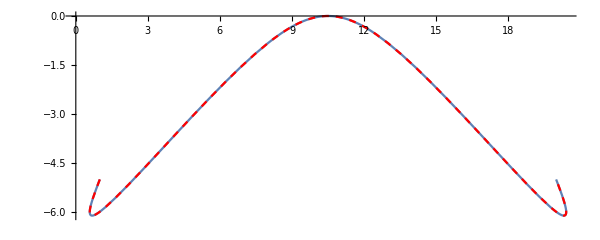

```mathematica
Show[ParametricPlot[{Re[x[t]/.solINI⟦1⟧/.par],Re[eta[t]/.solINI⟦1⟧/.par]},{t,0,1}],
ParametricPlot[{Re[x[t]/.solINI⟦2⟧/.par],Re[eta[t]/.solINI⟦2⟧/.par]},{t,0,1},PlotStyle->{Red, Dashed}],ImageSize->600]
```

## sqrt action from n-action

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
L=m/(2 n)(-T'[s]^2+X'[s]^2)-(m n)/2;
```

```mathematica
soln=Solve[D[L,n]==0,n]
```

{{n→-√(T'[s]^2-X'[s]^2)},{n→√(T'[s]^2-X'[s]^2)}}

```mathematica
Simplify[L/.soln⟦1⟧]
```

m √(T'[s]^2-X'[s]^2)